## Multiple scattering from Randomly placed cylinders

```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
directory= NotebookDirectory[]
```

/home/art/uom/study/Scattering/ScatterCylinder/v3/examples/

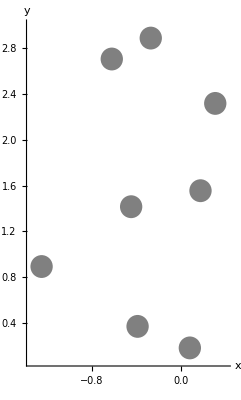

```mathematica
Generate randomly placed cylinders;
radius=0.1;
N0=3;
NParticles=8;
width=3;height=3;

Xs =GenerateParticles[NParticles,radius,{{-width/2,width/2},{0,height}}];
(*Calculate the volume fraction, volfrac, the mean distance, exp, and the standard deviation of the mean distance, std*)
{volfrac,exp,std}=StatsFromParticles[radius,Xs];
DrawScatterers[Xs,radius]
```

```mathematica
Measure the multiply scattered wave for a range of frequencies at {0,0};
ωs = Range[0.2,1.,0.2];

options={ 
"SourceWave"-> (I/4 HankelH1[0,#2 Norm[{#1[[1]],#1[[2]]}] /.Abs->Identity]&),
"BoundaryCondition"-> "Dirchlett"(*"BoundaryCondition"-> "Neumann"*)
};

(*Position of the scatterers and listeners/recievers*)
listeners={{0.,0.}};

(*Calcualted scatterd wave*)         
 FrequencyFromScatterers[listeners, Xs,radius, N0,ωs]
```

{{{0.2,0.0544315-0.0378675 ⅈ},{0.4,0.0645801-0.0605118 ⅈ},{0.6,0.0733239-0.0813153 ⅈ},{0.8,0.0815234-0.100139 ⅈ},{1.,0.0886901-0.117178 ⅈ}}}